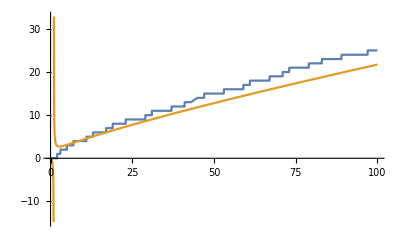

```mathematica
Plot[{PrimePi[x],x/Log[x]},{x,0,100}]
```

```mathematica
Animate[Plot[{PrimePi[x],x/Log[x]},{x,E,N},PlotLegends->Placed[{"Pi(x)","x/log(x)"},Left],PlotLabel->Style["Prime Number Theorem",20, Blue, Bold]],{N,100,10000},AnimationRate->100]
```

```mathematica
X:=Animate[Plot[{PrimePi[x],x/Log[x]},{x,E,N},PlotLegends->Placed[{"Pi(x)","x/log(x)"},Left],PlotLabel->Style["Prime Number Theorem",20, Blue, Bold]],{N,100,10000},AnimationRate->100]
```

```mathematica
Export["primes1.mp4", X, "mp4" ]
```

primes1.mp4

```mathematica
Animate[Plot[{PrimePi[x]/(x/Log[x]),1},{x,E,N},PlotLabel->Style["Pi(x)/(x/log(x))",20, Blue,Bold]],{N,100,1000000000000},AnimationRate->50000000000]
```

```mathematica
Y:=Animate[Plot[{PrimePi[x]/(x/Log[x]),1},{x,E,N},PlotLabel->Style["Pi(x)/(x/log(x))",20, Blue,Bold]],{N,100,1000000000000},AnimationRate->50000000000]
```

```mathematica
Export["primes2.mp4", Y, "mp4" ]
```

primes2.mp4